0.724989

0.68504

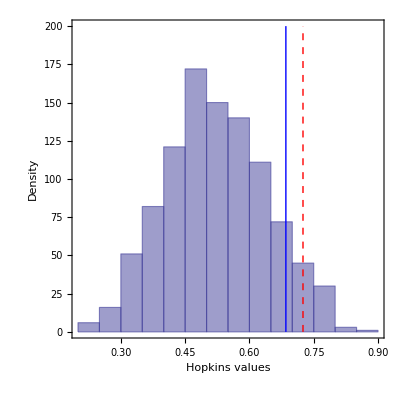

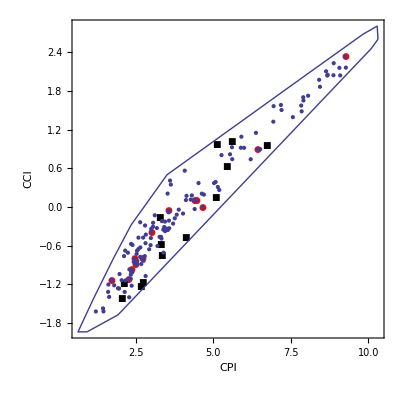

```mathematica
ClearAll[Matrix0,W,W1,Laplacean, EigenVec1, EigenVec2,PositionNearest,NC,prueba,prueba2]
(*directory="/Users/GAR/Documents/Thesis3"*)
(*directory="C:\\Users\\Natalia\\Documents\\Ipod Natty\\Thesis3";*)
directory="C:\Users\Natalia Villegas\Documents\Thesis3";
(*matlabDirectory ="/Applications/MATLAB_R2011b.app/bin/matlab"*)
SetDirectory[directory];



Needs["ComputationalGeometry`"]
inPolyQ[poly_,pt_]:=Graphics`Mesh`PointWindingNumber[poly,pt]=!=0
data0=Import["2008al2011ruido2.xls"];
data=data0[[3]];
(*data=Flatten[Import["CCI.mat"],1]*)




(*Se halla el convex Hull y se muestra gráficamente*)
convexHull=ConvexHull[data];
convexHull=AppendTo[convexHull,convexHull⟦1⟧];
pointsConvex=data⟦convexHull⟧;
center=Mean[data];
f=1.2;
int=Table[pointsConvex[[i,j]]*f+(1-f)*center[[j]],{i,Length[pointsConvex]-1},{j,2}];
convexHull2=ConvexHull[int];
convexHull2=AppendTo[convexHull2,convexHull2⟦1⟧];
Show[
ListPlot[data⟦convexHull⟧, Joined-> True, PlotRange->{{0,10},{-2.5,3}}],
ListPlot[Nearest[data,Mean[data]],ColorFunction->"Rainbow",PlotStyle->PointSize[Large]],
ListPlot[int⟦convexHull2⟧, Joined-> True, PlotRange->{{0,10},{-2.5,3}}]];


(*Se inicializan los parámetros de monte carlo*)
n=1000;
H=Table[{},{n}];
H0=Table[{},{n}];
m=Length[data];
samples2=Table[{RandomReal[{0,10}],RandomReal[{-2.5,2.5}]},{i,1,6009}];


Do[
m=Length[data]; (*pick m random points *)
samples2= samples2⟦Flatten[Position[inPolyQ[int[[convexHull2]],#]&/@ samples2, True]]⟧⟦1;;m⟧;
(*Se insertan los puntos aleatorios dentro de la ventana de muestreo*)
samples=Table[{RandomReal[{0,10}],RandomReal[{-2.5,2.5}]},{i,1,5008}];
(*samples=Table[{RandomReal[{-2.5,2.5}],RandomReal[{-2.5,2.5}]},{i,1,5009}];*)
samples = samples⟦Flatten[Position[inPolyQ[int[[convexHull2]],#]&/@ samples, True]]⟧⟦1;;m⟧;(*int[[convexHull2]]*)

(*Se insertan y se crean los puntos aleatorios para la hipótesis de aleatoriedad*)
samplesHo=Table[{RandomReal[{0,10}],RandomReal[{-2.5,2.5}]},{i,1,5008}];
(*samplesHo=Table[{RandomReal[{-2.5,2.5}],RandomReal[{-2.5,2.5}]},{i,1,5009}];*)
samplesHo=samplesHo⟦Flatten[Position[inPolyQ[data[[convexHull]],#]&/@ samplesHo, True]]⟧⟦1;;m⟧;

m=IntegerPart[Length[data]*(0.1)];
dataPoints=RandomSample[data,m];
 randomPoints=RandomSample[samples,m];
 
(*Se halla el estadístico de Hopkins*)                                             
H1=Table[EuclideanDistance[randomPoints⟦i⟧,Flatten[Nearest[data,randomPoints⟦i⟧],1]],{i,1,m}];
H2=Table[EuclideanDistance[dataPoints⟦i⟧,Flatten[Nearest[Cases[data,Except[#]],#]&/@ dataPoints,1]⟦i⟧],{i,1,m}];
H⟦k⟧=Total[H1^2]/Total[H1^2+H2^2];

(*Se halla el estadístico de Hopkins para la hipótesis de aleatoriedad*)  
dataPoints2=RandomSample[samples2,m];
randomPoints2=RandomSample[samplesHo,m];
H10=Table[EuclideanDistance[randomPoints2⟦i⟧,Flatten[Nearest[samples2,randomPoints2⟦i⟧],1]],{i,1,m}];
H20=Table[EuclideanDistance[dataPoints2⟦i⟧,Flatten[Nearest[Cases[samples2,Except[#]],#]&/@ dataPoints2,1]⟦i⟧],{i,1,m}];
H0⟦k⟧=Total[H10^2]/Total[H10^2+H20^2];,
{k,1,n}]

(*Se grafica el histograma de densidad de probabilidad con el valor del estadístico de hopkins para mis datos*)
Histogram[{H0,H}];
ho=Sort[H0];
Mean[H]
pho=ho[[Round[Length[ho]*0.90]]]
g8=Show[Histogram[{H0}],ListLinePlot[{{pho,0},{pho,200}},PlotStyle->Directive[Blue,Thick]],ListLinePlot[{{Mean[H],0},{Mean[H],200}},PlotStyle->Directive[Red,Dashed]],AspectRatio->1,Frame->True,FrameLabel->{"Hopkins values","Density"},Axes->False,LabelStyle->(FontSize->14)]
Export["Hopkins20102.eps",g8];

(*A continuación graficaré un ejemplo de los dataPoints y los randomPoints con la ventana de muestreo*)
Show[ListPlot[{dataPoints,randomPoints},PlotMarkers->Automatic,PlotStyle->{Directive[Red,PointSize[Large] 
],Directive[Black,PointSize[Large]]}],ListPlot[int⟦convexHull2⟧, Joined-> True],ListPlot[data,AspectRatio->Automatic],AspectRatio->1,PlotRange->All,Frame->True,FrameLabel->{"CPI","CCI"},FrameTicks->Automatic,AspectRatio->Automatic,Axes->False,LabelStyle->(FontSize->14)]
```

```mathematica
(*Timing[*)ClearAll[Matrix0,W,W1,Laplacean, EigenVec1, EigenVec2,PositionNearest,NC,prueba,prueba2,Partitions2]
(*directory="/Users/GAR/Documents/Thesis3"*)
(*directory="C:\\Users\\Natalia\\Documents\\Ipod Natty\\Thesis3";*)
directory="C:\Users\Natalia Villegas\Documents\Thesis3";
(*matlabDirectory ="/Applications/MATLAB_R2011b.app/bin/matlab"*)
SetDirectory[directory];


Matrix00=Import["2008al2011ruido2.xls"];
(*Muestra el conjunto de datos con la diagonal principal y sin particionarlos*)
g9=Show[ListLinePlot[{{0,-2.5},{10,2.5}}],ListPlot[Matrix00[[3]]],AspectRatio->1,PlotRange->All,Frame->True,FrameLabel->{"CPI","CCI"},FrameTicks->Automatic,Axes->False,LabelStyle->(FontSize->14)];
Export["CPICCI2010.eps",g9];
Export["Matrix0.xls",Matrix00];

u=2; (*Comienza todas la iteraciones para 2 clusters y posteriormente los hace para 3*)
v=10; (*Es el valor de k en "k-nearest neighbor graph" comienza en k=10 *)



PartitionedNetworks={};
Partitions={};
clusters={};
t=1;
clusters2={};
PartitionedNetworks2={};
Partitions2={};
t2=1;
Do[
Matrix0=Matrix00[[w]];
zz=Length[Matrix0];	
Do[
Do[
(*Parámetros*)

NC=u; (*Número de clusters*)
k=v;(*El valor de k del k-nearest neighbor graph para el CCI y CPI, respectivamente*)




(*Calculamos la función de similitud por medio de la transformación lineal*)
H=Table[EuclideanDistance[Matrix0[[i]],Matrix0[[j]]],{i,zz},{j,zz}];
max=Max[H];
min=Min[Table[Cases[H[[i]],Except[0.]],{i,zz}]] ;
H2=Table[max - min -1*H[[i]],{i,zz}];
W1=Table[If[i==j,0,H2[[i,j]]],{i,zz},{j,zz}];
(*W1=Table[(Matrix0[[i]].Matrix0[[j]])/(Norm[Matrix0[[i]]]^2+Norm[Matrix0[[j]]]^2-Matrix0[[i]].Matrix0[[j]]),{i,zz},{j,zz}];*)


(*Creamos la matriz de adyacencia W de acuerdo al "k-nearest neighbor graph"*)
M=Table[W1[[i,j]]->j,{i,zz},{j,zz}];
nearest1=MatrixForm[M];
m1=Table[Nearest[nearest1[[1,i]],Max[W1[[i]]],k],{i,zz}];
PositionNearest=MatrixForm[m1] ;
W=Table[0,{i,zz},{j,zz}]; 
Table[a=Count[PositionNearest[[1,PositionNearest[[1,i,j]]]],i];If[a==1,W[[i,PositionNearest[[1,i,j]]]]=W1[[i,PositionNearest[[1,i,j]]]],W[[i,PositionNearest[[1,i,j]]]]=0],{i,zz},{j,k}];


(*Hallamos la matriz de Grados D*)
A1={};
M8=Table[A1=Append[A1,Sum[W[[j,i]],{i,1,zz}]],{j,zz}];
degrees=Table[0,{i,1,zz},{j,1,zz}];
For[i=1,i<zz+1,i++,degrees[[i,i]]=M8[[zz,i]]];

(*Hallamos la matriz Laplaciana*)
Laplacean=degrees-W;

(*Calcula los valores propios de la matriz Laplaciana*)
EigenVal=Eigenvalues[Laplacean];
NrCompEig=Length[EigenVal];
NumEigvecs=Max[NC,2];


(*Ordena los valores propios y toma los NC primeros*)
EigenVal2=Sort[EigenVal];
ind=Ordering[EigenVal];
mm=Min[NumEigvecs,NrCompEig];
EigenVal3=Table[EigenVal2[[i]],{i,mm}];
Diferencias=Table[EigenVal2[[i]]-EigenVal2[[i-1]],{i,2,zz}];


(*Calcula los vectores propios de la matriz Laplaciana*)
EigenVec1=Transpose[Eigenvectors[Laplacean]];
EigenVec2=Table[EigenVec1[[j,ind[[i]]]],{j,zz},{i,zz}];
(*Ordena los vectores propios de acuerdo al orden de los valores propios*)
EigenVec=Table[EigenVec2[[j,i]],{j,zz},{i,NC}];

(*Método Kmeans para dividir los datos en clusters*)
Fi=ClusteringComponents[EigenVec,NC,1,Method->"KMeans"];
c3=Table[If[Fi[[i]]==j,Matrix0[[i]]],{j,NC},{i,zz}];
f2=Table[Cases[c3[[i]],Except[Null]],{i,NC}];
(*Crea la matriz para incluirla en el algoritmo de chou_su*)
MCS1=Table[If[Fi[[i]]==j,1,0],{i,zz},{j,NC}] ;



(*Asigna a cada cluster un color y una forma*)
color={Blue,Yellow,Red,Green,Pink,Brown,Black,Orange,Purple,Gray,White,Magenta};
c=Flatten[Table[If[Fi[[i]]==j,i->color[[j]]],{i,zz},{j,NC}]];
f=Cases[c,Except[Null]];
form={"Triangle","Square","Octagon","Rectangle","Pentagon","Hexagon","Triangle","Square","Octagon","Rectangle"};
c1=Flatten[Table[If[Fi[[i]]==j,i->form[[j]]],{i,zz},{j,NC}]];
f1=Cases[c1,Except[Null]];

W2=W;
Table[W2[[i,j]]=Infinity,{i,zz},{j,zz}];
(*Si deseo dibujar las aristas del grafo descomento la parte de abajo*)
(*Table[If[W[[i,j]]==0,W2[[i,j]]=Infinity,W2[[i,j]]=W[[i,j]]],{i,zz},{j,zz}];*)

(*Grafica los datos particionados (clusters)*)
g1=Show[ListLinePlot[{{0,-2.5},{10,2.5}},PlotStyle->{Black}],WeightedAdjacencyGraph[W2,VertexCoordinates->Matrix0,(*VertexLabels->Table[i->i,{i,zz}],*)VertexShapeFunction->f1,(*If[w==1,VertexSize->100,If[w==2,VertexSize->70,If[w==3,VertexSize->700,VertexSize->20]]]*)If[w==1,VertexSize->15,If[w==2,VertexSize->15,If[w==3,VertexSize->15,VertexSize->15]]],VertexStyle->f],AspectRatio->1,PlotRange->All,Frame->True,FrameLabel->{"CPI","CCI"},FrameTicks->Automatic,Axes->False,LabelStyle->(FontSize->14)];

(*Grafica los datos sin ser particionados*)
G8=Show[ListLinePlot[{{0,-2.5},{10,2.5}}, Frame->True,FrameLabel->{"CPI","CCI"},PlotStyle->{Black},Axes->False,AspectRatio->Automatic, LabelStyle->(FontSize->14)],ListPlot[Matrix0,Frame->True,Axes->False,FrameTicks->Automatic,PlotRange->{{10,2.5},{0,-2.5}}, AspectRatio->Automatic]];

PartitionedNetworks=Insert[PartitionedNetworks,g1,t];
Partitions=Insert[Partitions,f2,t];
clusters=Insert[clusters,Fi,t];t=t+1;
,{v,10,Length[Matrix0],5}];,{u,2,5,1}];

clusters2=Insert[clusters2,{clusters},t2];
PartitionedNetworks2=Insert[PartitionedNetworks2,{PartitionedNetworks},t2];
Partitions2=Insert[Partitions2,{Partitions},t2];PartitionedNetworks={};
Partitions={};
clusters={};t=1;t2=t2+1,{w,4}];

Partitions2=Flatten[Partitions2,1];
PartitionedNetworks2=Flatten[PartitionedNetworks2,1];
clusters2=Flatten[clusters2,1];
Export["clusters.xls",clusters2];



(*Exporta los clusters resultantes a Matlab y corre el código de Matlab*)
Run["Matlab -nosplash -wait -r Dunn"];




zz=Length[Matrix00[[1]]];	
MatthewsCoefficient={};
dunn=Flatten[Import["VGD.xls"],1];
total=Table[IntegerPart[(Length[Matrix00[[w]]]-10)/5+1],{w,4}];(*total se utilizaba cuando los años tenían tamaños diferentes*)
dunnMax=Table[dunn[[j,i +Sum[total[[l]],{l,k-1}]]],{j,4},{k,4},{i,total[[k]]}];
(*j representa el número de años, e i el número de particiones*)
maxDunnVal=Transpose[Table[Max[dunnMax[[i,j]]],{i,4},{j,4}]];
Export["DunnMax.xls",maxDunnVal];
positionMaxDunn=Partition[Flatten[Transpose[Table[Position[dunnMax[[i,j]],Max[dunnMax[[i,j]]]],{i,4},{j,4}]]],4];
(*Do[If[countries[[i,m]]==countries[[k,n]],fi=AppendTo[fi,fi1[[m]]];,fii=AppendTo[fii,fi2[[n]]];],{m,total[[i]]},{n,total[[k]]}];*)

Do[
fi1=clusters2[[p,total[[p]]*(r-1)+positionMaxDunn[[p,r]]]]; (*total*(j-1) me permite diferenciar entre un # de clusters y otro*)
fi2=clusters2[[q,total[[q]]*(r-1)+positionMaxDunn[[q,r]]]];
(*PROCESO PARA CALCULAR EL COEFICIENTE DE CORRELACIÓN DE MATTHEWS*)
(*Comparación entre los datos particionados del CCI en 2 clusters contra los particionados del CPI en 2 clusters*)

NC=r+1; (*Número de clusters*)

cont=0;

prueba=Table[0,{i,NC},{h,NC},{j,4}];
(*Calculamos la matriz de confusión*)
Do[If[fi2[[j]]==h,If[fi1[[j]]==i, cont=cont+1]];prueba[[h,i,1]]=cont ,{h,NC},{i,NC},{j,zz}];

prueba2=Table[0,{i,NC},{h,NC},{j,4}];
Do[If[h==1&& i==1, prueba2[[h,i,1]]=prueba[[h,i,1]], If[i==1 ,prueba2[[h,i,1]]=prueba[[h,i,1]]-prueba[[h-1,NC,1]],prueba2[[h,i,1]]=prueba[[h,i,1]]-prueba[[h,i-1,1]]]],{h,NC},{i,NC}];
Do[prueba2[[h,i,2]]=Count[fi2,h]-prueba2[[h,i,1]];prueba2[[h,i,3]]=Count[fi1,i]-prueba2[[h,i,1]];prueba2[[h,i,4]]=zz-prueba2[[h,i,1]]-prueba2[[h,i,2]]-prueba2[[h,i,3]],{h,NC},{i,NC}];
prueba2; (*Matriz de confusión con la que se halla el coefieciente de correlación*)

(*Hallamos el coeficiente de correlacíon de Matthews*)
MatthewsCorrelationCoefficient=Table[0,{i,NC},{h,NC}];
Do[MatthewsCorrelationCoefficient[[h,i]]=((prueba2[[h,i,1]]*prueba2[[h,i,4]])-(prueba2[[h,i,3]]*prueba2[[h,i,2]]))/(((prueba2[[h,i,1]]+prueba2[[h,i,3]])*(prueba2[[h,i,1]]+prueba2[[h,i,2]])*(prueba2[[h,i,4]]+prueba2[[h,i,3]])*(prueba2[[h,i,4]]+prueba2[[h,i,2]]))^(1/2)),{h,NC},{i,NC}];

MatthewsCorrelationCoefficient=N[MatthewsCorrelationCoefficient] ;

MatthewsCoefficient=AppendTo[MatthewsCoefficient,MatthewsCorrelationCoefficient] ;(*Coeficiente de correlación de Matthews entre clusters*)
,{p,3},{q,p+1,4},{r,2}]
clusters2[[1,total[[1]]*(1-1)+positionMaxDunn[[1,1]]]];
clusters2[[3,total[[3]]*(1-1)+positionMaxDunn[[3,1]]]];


MatthewsCoefficient
t



(*Muestra las mejores particiones según el criterio del índice generalizado de Dunn*)
PartitionedNetworks2;
partitions=Table[PartitionedNetworks2[[p,total[[p]]*(r-1)+positionMaxDunn[[p,r]]]],{p,4},{r,2}]




numberOfYears=4;
partitions3=Table[Partitions2[[p,total[[p]]*(r-1)+positionMaxDunn[[p,r]]]],{p,4},{r,2}];
```

Transpose::nmtx: The first two levels of the one-dimensional list SparseArray[Automatic, {132}, 0, {1, {{0, 0}, {}}, {}}] cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

{{{0.684296,-0.684296},{-0.684296,0.684296}},{{0.462106,-0.254097,-0.351739},{-0.451334,0.50772,0.15577},{-0.175407,-0.0991769,0.27504}},{{0.950654,-0.950654},{-0.950654,0.950654}},{{0.687169,-0.35511,-0.5395},{-0.785105,0.658221,0.433719},{-0.11466,-0.158614,0.247636}},{{0.950654,-0.950654},{-0.950654,0.950654}},{{0.709483,-0.366642,-0.557019},{-0.785105,0.658221,0.433719},{-0.137665,-0.151915,0.269452}},{{0.732912,-0.732912},{-0.732912,0.732912}},{{0.600014,-0.365644,-0.393863},{-0.437481,0.600004,0.0358748},{-0.314143,-0.0962404,0.42304}},{{0.732912,-0.732912},{-0.732912,0.732912}},{{0.596062,-0.37991,-0.378701},{-0.437481,0.600004,0.0358748},{-0.311871,-0.0849422,0.41199}},{{0.901308,-0.901308},{-0.901308,0.901308}},{{0.904624,-0.557019,-0.562116},{-0.5395,1.,-0.240973},{-0.583255,-0.230796,0.871441}}}

1

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

1

```mathematica
(*Coeficientes de correlación de Matthews (se demoró 4:04 min)*)
{{{0.7039252336448598,-0.7039252336448598},{-0.7039252336448598,0.7039252336448598}},{{0.5296542676838147,-0.2654356850830906,-0.4110489040270967},{-0.3623245827536492,0.5289595774275506,0.06890818588289359},{-0.3234761061041093,-0.09514871879602263,0.4082482904638631}},{{1.,-1.},{-1.,1.}},{{0.8290669532823414,-0.35511041211421746,-0.6803091303374613},{-0.6257616352380223,0.6582212920597776,0.27504013461143384},{-0.41570957627313115,-0.15861353514209012,0.5468569153752658}},{{0.9273725270140347,-0.9273725270140347},{-0.9273725270140347,0.9273725270140347}},{{0.8825573136595964,-0.39146270653262055,-0.7159881488701807},{-0.553141592940038,0.7446368838013963,0.14363447023631967},{-0.5681729091594555,-0.15191493468985848,0.7077771929419521}},{{0.7039252336448598,-0.7039252336448598},{-0.7039252336448598,0.7039252336448598}},{{0.5985284094005363,-0.34641016151377546,-0.4122172690743038},{-0.4551690430401234,0.5621481263959848,0.09226870278438683},{-0.29716851251144466,-0.08574641335676547,0.3955376290181996}},{{0.7329115682120448,-0.7329115682120448},{-0.7329115682120448,0.7329115682120448}},{{0.6182944458806288,-0.38938629236965366,-0.40247590661989263},{-0.4225889384577596,0.6462226994596151,-0.006396930210072014},{-0.3696705844606645,-0.07468612698009627,0.4683558632029551}},{{0.9273725270140347,-0.9273725270140347},{-0.9273725270140347,0.9273725270140347}},{{0.907137273074124,-0.5947281123459451,-0.5324758448368663},{-0.47689070987373994,0.8839493535420053,-0.21300789497877504},{-0.658148215781045,-0.030697023792642903,0.785114530159098}}}
```

1

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}